```mathematica
N[(π-(3 √3)/4)]
N[(π+(3 √3)/4)]
N[4π(1-.75^2)]
N[π+(3 √3)/4+(3 √3)/(4π)]
```

1.84255

4.44063

5.49779

4.85413

```mathematica
N[(√3)/(4π)]
```

0.137832

```mathematica
N[(√3)/4]
```

0.433013

```mathematica
N[1-(√3)/(4π)]
```

0.862168

```mathematica
Simplify[((1-((√3)/(4π)p)^k)(3/4)(4.8541)p^2)/((1-(√3)/(4π))^k 3p)]
```

-1.21353 p (-√3+4 π)^-k (3^(k/2) p^k-1. (4 π)^k)

```mathematica
N[π*0.01]
```

0.0314159

```mathematica
N[1/(2*300*π*0.01*8)]
```

0.00663146

```mathematica
N[√(1/(4π))]
```

0.282095

```mathematica
Simplify[Solve[(√3)/(4π)*p==P_U*(1-(√3)/(4π))^k+0.175*p*(1-(1-(√3)/(4π))^k), P_U]]
```

{{P_U→(-0.0371678+0.175 0.862168^k) ⅇ^(0.148305 k) p}}

```mathematica
Cos[π/3]
```

1/2

```mathematica
N[(0.1723*0.9777+0.1728*0.9751+0.1596*0.9806+0.1727*0.9912+0.1669*0.9911)/(0.9777+0.9751+0.9806+0.9912+0.9911)]
```

0.168858

```mathematica
Log[1-(√3)/(4π)/0.1689]/Log[1-(√3)/(4π)]
```

11.4165

```mathematica
Solve[0.1689+((√3)/(4π)-0.1689)(1-(√3)/(4π))^-k==0,k]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{k→11.4165}}

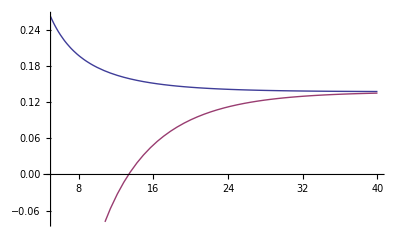

```mathematica
Plot[{(√3)/(4π)/(1-(1-(√3)/(4π))^k),((1-(√3)/(4 π))^k-(√3)/(4 π))/((1-(√3)/(4 π))^k-1)},{k,5,40}]
```

```mathematica
Solve[x^11==0.359,x]
```

{{x→-0.87417-0.256679 ⅈ},{x→-0.87417+0.256679 ⅈ},{x→-0.596627-0.688544 ⅈ},{x→-0.596627+0.688544 ⅈ},{x→-0.129659-0.901801 ⅈ},{x→-0.129659+0.901801 ⅈ},{x→0.378474-0.828743 ⅈ},{x→0.378474+0.828743 ⅈ},{x→0.766445-0.492564 ⅈ},{x→0.766445+0.492564 ⅈ},{x→0.911075}}

```mathematica
Sin[π-θ]
```

Sin[θ]

```mathematica
Gamma[2]
```

1

```mathematica
N[∫_0^(2π/3) (1-(θ-Sin[θ])/π)^k*2/3 Sin[θ]ⅆθ]
```

```mathematica
Plot[∫_0^(2π/3) (1-(θ-Sin[θ])/π)^k*2/3 Sin[θ]ⅆθ, {k,2,10}, PlotPoints->9]
```

$Aborted

```mathematica
N[∫_0^(2π/3) (1-(θ-Sin[θ])/π)^31*2/3 Sin[θ]ⅆθ]
```

45.8561

{{1,0.862168},{2,0.75613},{3,0.673142},{4,0.607086},{5,0.553643},{6,0.509726},{7,0.473108},{8,0.44216},{9,0.41568},{10,0.392767},{11,0.372737},{12,0.355069},{13,0.339355},{14,0.325277},{15,0.31258},{16,0.301063},{17,0.290558},{18,0.280932},{19,0.272072},{20,0.263885},{21,0.256292},{22,0.249233},{23,0.242636},{24,0.236162},{25,0.23446},{26,0.268766},{27,0.0999494},{28,-0.539183},{29,-2.25928},{30,-16.1986},{31,45.8561},{32,-6827.38},{33,3303.08},{34,1.25719×10^6},{35,-1.02244×10^7},{36,1.36386×10^7},{37,2.4582×10^8},{38,2.40977×10^10},{39,-9.983×10^10},{40,-3.29146×10^12}}

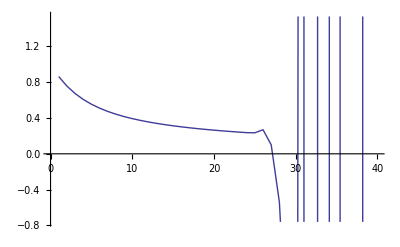

```mathematica
pyx = Table[{k,N[∫_0^(2π/3) (1-(θ-Sin[θ])/π)^k*2/3 Sin[θ]ⅆθ]}, {k,1,40}];
Print[pyx];ListLinePlot[pyx]
```

```mathematica
PU[r_,k_]:={∫_0^(2π/3) r^2(θ-Sin[θ])(1-(θ-Sin[θ])/π)^k*2/3 Sin[θ]ⅆθ};
 (* k = Ceil[N[π*0.08*0.08*300]] *)
N[PU[0.08,6]]
```

{0.000736254-6.23963×10^-19 ⅈ}

```mathematica
Simplify[∫_0^(2ArcCos[Sqrt[k]/2]) r*r(theta-Sin[theta])(2/(4-k)Sin[theta])ⅆtheta]
```

(r^2 (-√(-(-4+k) k) (2+k)+8 (-1+k) ArcSec[2/(√k)]))/(4 (-4+k))

```mathematica
∫_0^(2π/3) r*r(theta-Sin[theta])(2/3Sin[theta])ⅆtheta
```

(√3 r^2)/4

```mathematica
Unset[r]
∫_(2π/3)^π r*r(theta-Sin[theta])(2Sin[theta])ⅆtheta
```

(-(3 √3)/4+π) r^2

```mathematica
r^2(2π/3-Sin[2π/3])
```

(-(√3)/2+(2 π)/3) r^2

```mathematica
Simplify[2(r^2 ArcCos[r/(2r)]-r(r/2)√(1-(r/(2r))^2))]
2(r^2 ArcCos[(2r)/(2r)]-r((2r)/2)√(1-((2r)/(2r))^2))
```

1/6 (-3 √3+4 π) r^2

0

```mathematica
N[∫_0^(2π/3) (1-(theta-Sin[theta])/π)^2 ⅆtheta]
Simplify[N[∫_0^(2π) ∫_r^(2r) (1-2(r^2 ArcCos[x/(2r)]-r(x/2)√(1-(x/(2r))^2))/πr^2)^2 ⅆxⅆρ]]
```

1.70368

6.28319 r+(2.45515 r^5)/πr^4+(10.8828 r^3)/πr^2-(17.2122 √(1/r^2) r^4)/πr^2

```mathematica
Unset[r]
(* The following is the closest approximation but r is unaccounted for, so it's still wrong *)
(* n = 3: 1.5~1.6 *)
N[ (4*π-2*π*∫_0^(2*π/3) (3/4)(1-(θ-Sin[θ])/π)^2 ⅆθ)/π]
(* n = 4: 1.75 *)
N[ (4*π-2*π*∫_0^(2*π/3) (3/4)(1-(θ-Sin[θ])/π)^3 ⅆθ)/π]
(* n = 5: 1.95 *)
N[ (4*π-2*π*∫_0^(2*π/3) (3/4)(1-(θ-Sin[θ])/π)^4 ⅆθ)/π]
(* n = 6: 2 *)
N[ (4*π-2*π*∫_0^(2*π/3) (3/4)(1-(θ-Sin[θ])/π)^5 ⅆθ)/π]
(* n = 7: 2.2 *)
N[ (4*π-2*π*∫_0^(2*π/3) (3/4)(1-(θ-Sin[θ])/π)^6 ⅆθ)/π]
(* n = 8: 2.25-2.29 *)
N[ (4*π-2*π*∫_0^(2*π/3) (3/4)(1-(θ-Sin[θ])/π)^7 ⅆθ)/π]
```

1.44448

1.64468

1.80471

1.93488

2.04254

2.13298

```mathematica
Unset[r]
Simplify[π r^2 +∫_0^(2π) ∫_r^(2r) x(1-(1-2(r^2 ArcCos[x/(2r)]-r(x/2)√(1-(x/(2r))^2))/(π r^2))^2)ⅆxⅆρ]
```

(r^2 (27+π^2 (14-8 √(1/r^2) r)-3 √3 π (-2+√(1/r^2) r)))/(6 π)

```mathematica
(* THE FOLLOWING IS CORRECT *)
(* n = 2: 1.29 *)Simplify[N[(4π r^2- ∫_0^(2π) ∫_r^(2r) x(1-2(r^2 ArcCos[x/(2r)]-r(x/2)√(1-(x/(2r))^2))/(π r^2))ⅆxⅆρ)/(π r^2)]]
```

1.4135

```mathematica
(* n = 3: 1.58 *)
Simplify[N[(4π r^2- ∫_0^(2π) ∫_r^(2r) x(1-2(r^2 ArcCos[x/(2r)]-r(x/2)√(1-(x/(2r))^2))/(π r^2))^2 ⅆxⅆρ)/(π r^2)]]
```

1.73161

```mathematica
(* n = 4: 1.75 *)Simplify[N[(4π r^2- ∫_0^(2π) ∫_r^(2r) x(1-2(r^2 ArcCos[x/(2r)]-r(x/2)√(1-(x/(2r))^2))/(π r^2))^3 ⅆxⅆρ)/(π r^2)]]
```

1.98057

```mathematica
(* n = 5: 1.95 *)Simplify[N[(4π r^2- ∫_0^(2π) ∫_r^(2r) x(1-2(r^2 ArcCos[x/(2r)]-r(x/2)√(1-(x/(2r))^2))/(π r^2))^4 ⅆxⅆρ)/(π r^2)]]
```

2.17874

```mathematica
(* n = 6: 2.05 *)Simplify[N[(4π r^2- ∫_0^(2π) ∫_r^(2r) x(1-2(r^2 ArcCos[x/(2r)]-r(x/2)√(1-(x/(2r))^2))/(π r^2))^5 ⅆxⅆρ)/(π r^2)]]
```

2.33907

```mathematica
(* n = 7: 2.2 *)Simplify[N[(4π r^2- ∫_0^(2π) ∫_r^(2r) x(1-2(r^2 ArcCos[x/(2r)]-r(x/2)√(1-(x/(2r))^2))/(π r^2))^6 ⅆxⅆρ)/(π r^2)]]
```

2.47082

```mathematica
(* n = 8: 2.25 *)Simplify[N[(4π r^2- ∫_0^(2π) ∫_r^(2r) x(1-2(r^2 ArcCos[x/(2r)]-r(x/2)√(1-(x/(2r))^2))/(π r^2))^7 ⅆxⅆρ)/(π r^2)]]
```

2.58068

```mathematica
N[1+(3 √3)/(4π)]
```

1.4135

```mathematica
N[1+(3 √3)/(4π)+((3 √3)/(4π))^2]
```

1.58448

```mathematica
N[1+(3 √3)/(4π)+((3 √3)/(4π))^2+((3 √3)/(4π))^3]
```

1.65518

```mathematica
N[1+(3 √3)/(4π)+((3 √3)/(4π))^2+((3 √3)/(4π))^3+((3 √3)/(4π))^4]
```

1.68441

```mathematica
N[1+(√3)/(2π)]
```

1.27566

```mathematica
N[1+(√3)/(2π)+((√3)/(2π))^2]
```

1.35166

```mathematica
N[1+(√3)/(2π)+((√3)/(2π))^2+((√3)/(2π))^3]
```

1.3726

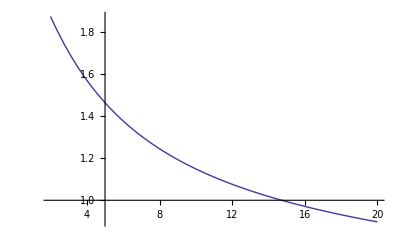

```mathematica
Plot[N[∫_0^(2π/3) (1-(theta-Sin[theta])/π)^(x-1)ⅆtheta],{x,2,20}]
```

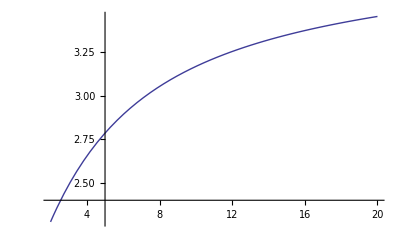

```mathematica
Plot[N[4-2(2/3)∫_0^(2π/3) (1-(theta-Sin[theta])/π)^(x-1)Sin[theta]ⅆtheta],{x,2,20}]
```